```mathematica
SetDirectory["L:/moose/trunk/wallaby/doc/tests/data"]
```

L:\moose\trunk\wallaby\doc\tests\data

```mathematica
p0=2*10^6;
bulk = 10^6;
dens0=1000;
rho[p_] := dens0*Exp[p/bulk];
ll=100;
rhoAtEnd=2*dens0;
cc=(rho[p0]-rhoAtEnd)/ll/dens0;
perm=10^-15;
visc = 10^-3;
pEnviron=0.0;
porosity=0.1;
alpha=perm*bulk/visc/porosity;

flux[p_] :=cc*bulk*perm/visc*(rho[p]-rho[pEnviron]);
```

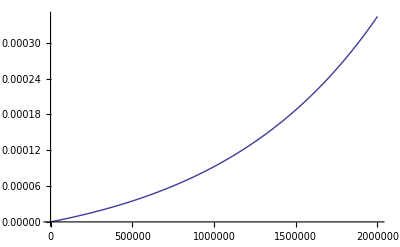

```mathematica
Plot[flux[p],{p,0,2*10^6}]
```

```mathematica
ClearAll[kn];
kn[n_] :=kn[n]=k/.FindRoot[ll*cc*Tan[k]+k==0,{k,(2n-1)*Pi/2+0.01}];
rhoInit[x_]:=rho[p0];

ClearAll[a];
a[n_]:=a[n]=Integrate[(rhoInit[x]-rhoInit[0]+(rhoInit[0]-rho[pEnviron])*cc*x/(1+ll*cc))*Sin[kn[n]*x/ll],{x,0,ll}]/Integrate[Sin[kn[n]*x/ll]^2,{x,0,ll}];

answer[x_,t_] := rhoInit[0]-(rhoInit[0]-rho[pEnviron])*cc*x/(1+ll*cc)+Sum[a[n]Sin[kn[n]x/ll]Exp[-kn[n]^2*alpha*t/ll^2],{n,1,20}];
pressure[x_,t_]:=bulk*Log[answer[x,t]/dens0];
```

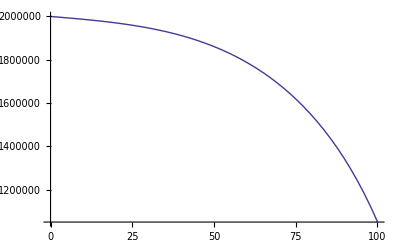

```mathematica
Plot[Evaluate[pressure[x,10^8]],{x,0,ll},PlotRange->All]
```

```mathematica
Export["nc02_analytic.txt",{#,Evaluate[pressure[#,10^12]]}&/@Range[100],"Table"]
```

nc02_analytic.txt